### 3rd example support vector machine

In this example we revisit the previous example and modify it slightly by moving around the parabola and ellipse.

```mathematica
f2b[x_]:=0.2 (x-5)^2+1
f3b[x_]:=(x[[1]]-5)^2+0.5(x[[2]]+3)^2
```

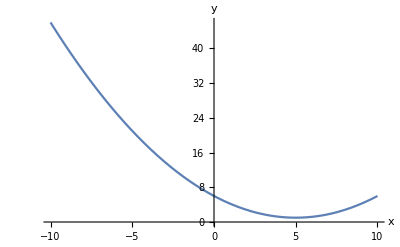

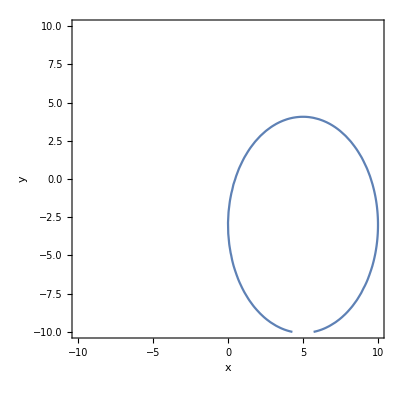

```mathematica
Plot[f2b[x],{x,-10,10},AxesLabel->{"x","y"}]
ContourPlot[f3b[{x,y}]==25,{x,-10,10},{y,-10,10},FrameLabel->{"x","y"}]
```

First of all we need to generate some random data points and our training data set (as before):

```mathematica
alldata[n_]:=RandomReal[{-10,10},{n,2}]
```

```mathematica
ts2b[datax_]:=Module[{data=datax},data2={};Do[If[(f2b[data[[i,1]]]-data[[i,2]])≥0,data2=Append[data2,{data[[i]],1}],data2=Append[data2,{data[[i]],-1}]],{i,1,Length[data]}];data2]
ts3b[datax_]:=Module[{data=datax},data2={};Do[If[(f3b[data[[i]]])<=25,data2=Append[data2,{data[[i]],1}],data2=Append[data2,{data[[i]],-1}]],{i,1,Length[data]}];data2]
```

```mathematica
gb[datax_]:=Module[{data=datax},g={};b={};Do[If[data[[i,2]]==1,g=Append[g,data[[i,1]]],b=Append[b,data[[i,1]]]],{i,1,Length[data]}];{g,b}]
```

Let’s look at our data:

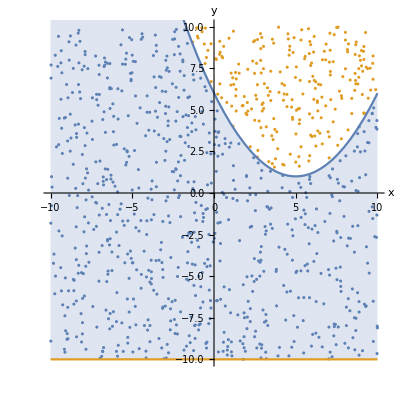

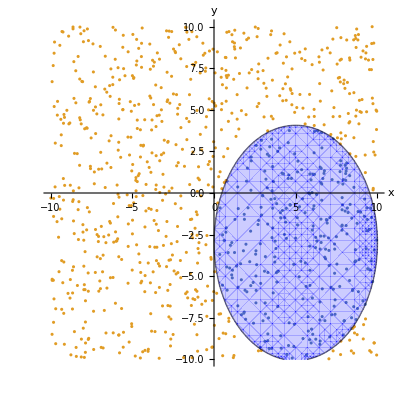

```mathematica
Show[ListPlot[gb[ts2b[alldata[1000]]],PlotRange->{{-10,10},{-10,10}},AspectRatio->1,AxesLabel->{"x","y"}],Plot[{f2b[x],-10},{x,-10,10},Filling->{1->{2}}]]
Show[ListPlot[gb[ts3b[alldata[1000]]],PlotRange->{{-10,10},{-10,10}},AspectRatio->1,AxesLabel->{"x","y"}],ContourPlot[f3b[{x,y}],{x,-10,10},{y,-10,10},Contours->{25},ContourShading->{Directive[Blue,Opacity[0.2]],None}]]
```

Let’s look at the kernel map from before

```mathematica
kmc[x_]:={x[[1]]^2,x[[2]]};
```

```mathematica
d3=alldata[1000];
d3a=gb[ts2b[d3]][[1]];
d3b=gb[ts2b[d3]][[2]];
```

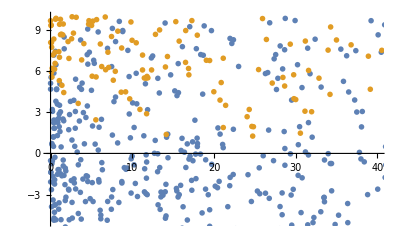

```mathematica
ListPlot[{Table[kmc[d3a[[i]]],{i,1,Length[d3a]}],Table[kmc[d3b[[i]]],{i,1,Length[d3b]}]},PlotRange->{{0,40},{-5,10}},PlotStyle->PointSize[0.01]]
```

This map does not separate our data nicely anymore. We can look at the data in 3D with a different kernel map.

```mathematica
kmb2[x_]:={x[[1]]^2,x[[1]],x[[2]]};
```

```mathematica
ListPointPlot3D[{Table[kmb2[d3a[[i]]],{i,1,Length[d3a]}],Table[kmb2[d3b[[i]]],{i,1,Length[d3b]}]},AxesLabel->{"x^2"," x y"," y^2"}]
```

-Graphics3D-

```mathematica
c=Classify[<|1->d3a,-1->d3b|>, Method->{"SupportVectorMachine","KernelType"->"Linear"}]
```

ClassifierFunction[…]

```mathematica
Plot3D[{
c[{x,y},"Probability"->1],
c[{x,y},"Probability"->-1]
},
{x,-10,10},{y,-10,10},
 Exclusions->None]
```

-Graphics3D-

Doesn’t look too good, let’s quantify how bad this is:

test data set:

```mathematica
t3=alldata[10000];
t3a=gb[ts2b[t3]][[1]];
t3b=gb[ts2b[t3]][[2]];
```

```mathematica
N[Count[c[t3a],1]/Length[t3a]]
N[Count[c[t3a],-1]/Length[t3a]]
N[Count[c[t3b],1]/Length[t3b]]
N[Count[c[t3b],-1]/Length[t3b]]
```

0.9714

0.0285997

0.25169

0.74831

Now, let’s do the same thing with the kernel map:

```mathematica
c2=Classify[<|1->Table[kmb2[d3a[[i]]],{i,1,Length[d3a]}],-1->Table[kmb2[d3b[[i]]],{i,1,Length[d3b]}]|>, Method->{"SupportVectorMachine","KernelType"->"Linear"}]
```

ClassifierFunction[…]

```mathematica
N[Count[c2[Table[kmb2[t3a[[i]]],{i,1,Length[t3a]}]],1]/Length[t3a]]
N[Count[c2[Table[kmb2[t3a[[i]]],{i,1,Length[t3a]}]],-1]/Length[t3a]]
N[Count[c2[Table[kmb2[t3b[[i]]],{i,1,Length[t3b]}]],1]/Length[t3b]]
N[Count[c2[Table[kmb2[t3b[[i]]],{i,1,Length[t3b]}]],-1]/Length[t3b]]
```

0.995171

0.00482853

0.0436817

0.956318

Still, the points in the parabola are classified better but not yet perfectly. Empirically (check!), this is related to the amount of data in the different training sets. There are not enough points in set b.

```mathematica
Length[d3a]
Length[d3b]
```

812

188

Let’s do the same modification for the ellipsoid

Let’s look at the kernel map from before

```mathematica
kmb[x_]:={x[[1]]^2,x[[2]]^2};
```

```mathematica
d3=alldata[1000];
d3a=gb[ts3b[d3]][[1]];
d3b=gb[ts3b[d3]][[2]];
```

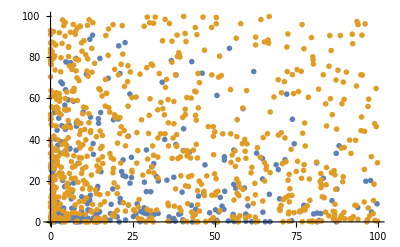

```mathematica
ListPlot[{Table[kmb[d3a[[i]]],{i,1,Length[d3a]}],Table[kmb[d3b[[i]]],{i,1,Length[d3b]}]},PlotStyle->PointSize[0.01]]
```

Let’s modify the map

```mathematica
kmb2[x_]:={x[[1]]^2,x[[1]],x[[1]]x[[2]],x[[2]],x[[2]]^2};
```

```mathematica
c4=Classify[<|1->Table[kmb2[d3a[[i]]],{i,1,Length[d3a]}],-1->Table[kmb2[d3b[[i]]],{i,1,Length[d3b]}]|>, Method->{"SupportVectorMachine","KernelType"->"Linear"}]
```

ClassifierFunction[…]

```mathematica
t3=alldata[10000];
t3a=gb[ts3b[t3]][[1]];
t3b=gb[ts3b[t3]][[2]];
```

```mathematica
N[Count[c4[Table[kmb2[t3a[[i]]],{i,1,Length[t3a]}]],1]/Length[t3a]]
N[Count[c4[Table[kmb2[t3a[[i]]],{i,1,Length[t3a]}]],-1]/Length[t3a]]
N[Count[c4[Table[kmb2[t3b[[i]]],{i,1,Length[t3b]}]],1]/Length[t3b]]
N[Count[c4[Table[kmb2[t3b[[i]]],{i,1,Length[t3b]}]],-1]/Length[t3b]]
```

0.9594

0.0405999

0.0228461

0.977154

And we are doing pretty well now...